# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documents/Wolfram Mathematica/QKT/D2 alfa 0.84, k By parity

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[8]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
radius=0.5;
delta=0.01;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
region=gridPoints;
region//Length
```

10201

```mathematica
radius=1.99999;
delta=0.03;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

14153

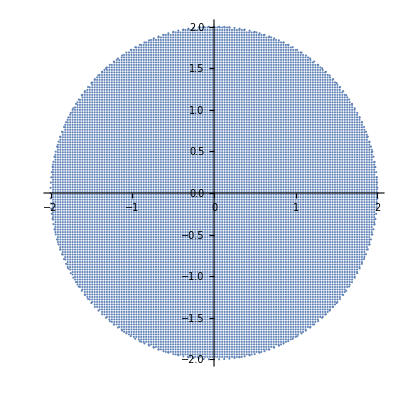

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
Clear[J];
J=1500;
α=0.84;
τ=1;

Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];
```

## Method

```mathematica
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
klist=Range[0.1,10,0.1];
```

```mathematica
Do[

mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^4],{i,cohesM}];
newd2M=Transpose[{region[[All,1]],region[[All,2]],-Log[d2M]/Log[J+1]}];
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newd2M,PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]];
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".m",newd2M];

,{k,klist}]
```

```mathematica
NotebookSave[]
```

```mathematica
NotebookClose[]
```

# Distributions of D2

```mathematica
Clear[J];
J=1500;
α=0.84;
τ=1;
dq=0.02;
```

```mathematica
klist=Range[10.1,23.4,0.1];
```

```mathematica
data=Table[Import["/home/miguel/Documents/Wolfram Mathematica/QKT/D2 alfa 0.84, k By parity/d2plus_zoom_J_1500_alpha_0.84_k_"<>ToString[k]<>"_dq_0.02.m"],{k,klist}];
```

```mathematica
data//Dimensions
```

{134,31602,3}

```mathematica
q=60;
ListDensityPlot[data[[q]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]]<>", dq = "<>ToString[dq],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

```mathematica
d2s=data[[q]][[All,3]];
newprsa=Table[If[i>=0.7,Exp[i*Log[J+1]]],{i,d2s}];
```

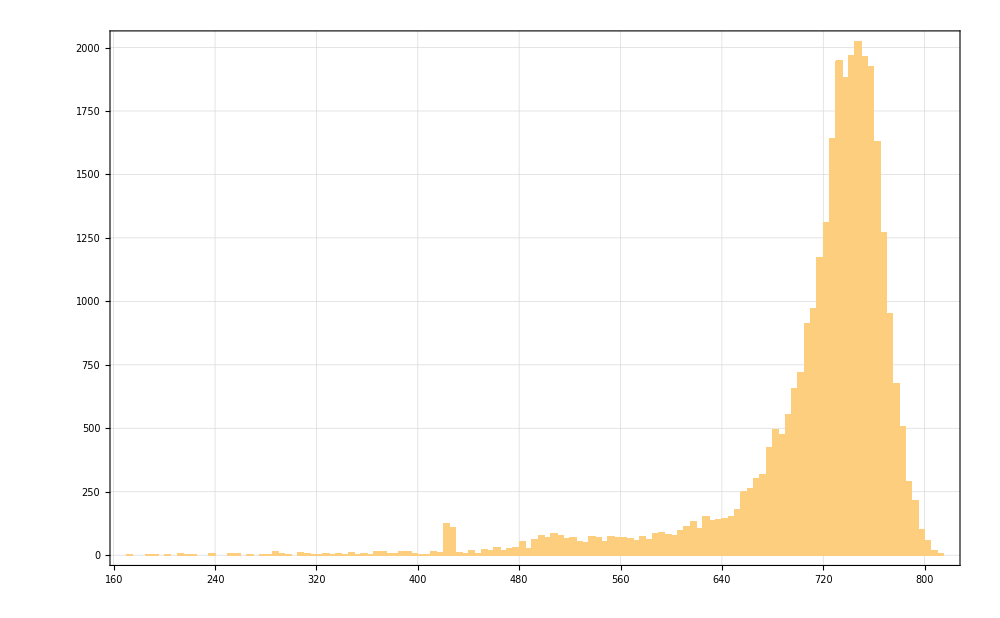

```mathematica
Histogram[newprsa,100,PlotRange->All,PlotTheme->"Detailed",ImageSize->1000]
```

```mathematica
q=80;
ListDensityPlot[data[[q]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]]<>", dq = "<>ToString[dq],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

```mathematica
d2s=data[[1]][[All,3]];
newprsb=Table[If[i>=0.7,Exp[i*Log[J+1]]],{i,d2s}];
```

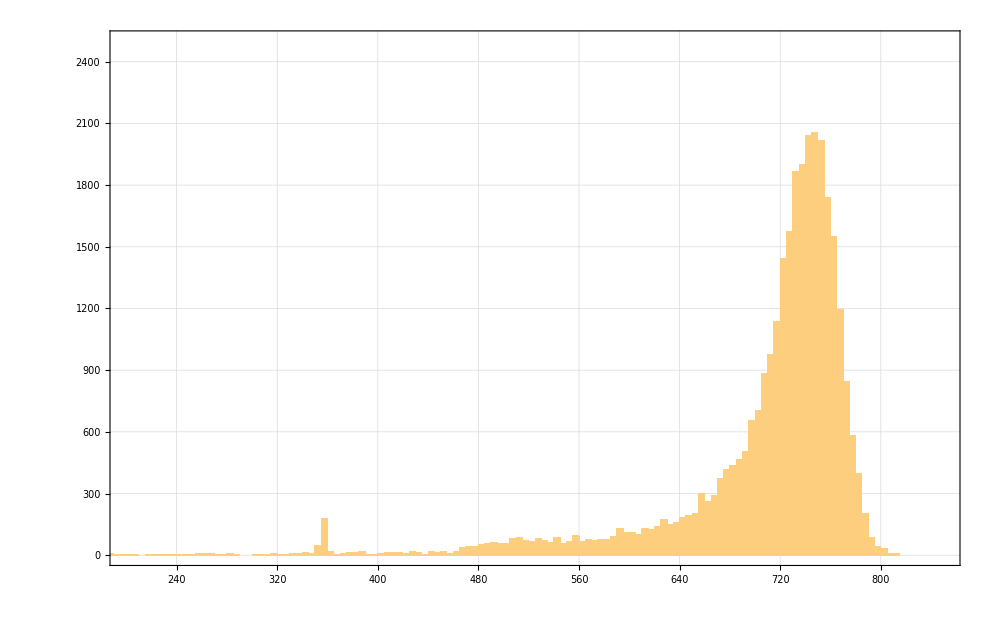

```mathematica
Histogram[newprsb,100,PlotRange->{{200,850},{0,2500}},PlotTheme->"Detailed",ImageSize->1000]
```

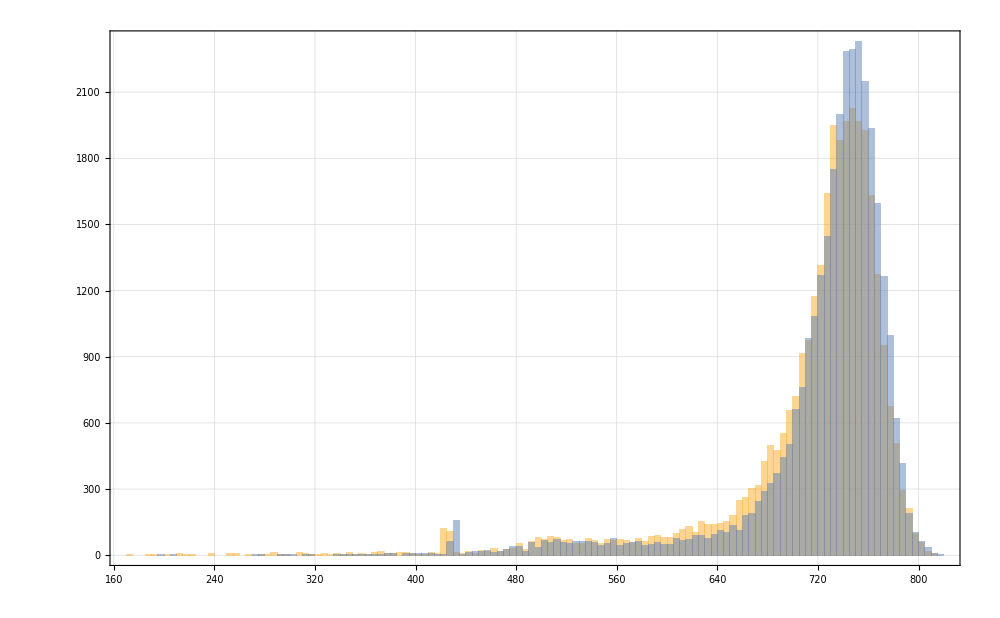

```mathematica
Histogram[{newprsa,newprsb},100,PlotRange->All,PlotTheme->"Detailed",ImageSize->1000]
```

```mathematica
plots={};
Do[

d2s=data[[q]][[All,3]];
newprsa=Table[If[i>=0.7,Exp[i*Log[J+1]]],{i,d2s}];
plot=Histogram[newprsa,100,PlotLabel->Style["k = "<>ToString[klist[[q]]],25,Black],PlotRange->{{200,850},{0,2500}},PlotTheme->"Detailed",ImageSize->1000];
AppendTo[plots,plot];

,{q,Length[data]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```